# Using Mathematica for Scalar 1st Order ODEs (Bifurcations)

## Solving Differential Equations with various initial conditions

Let’s solve the initial value problem

y' = y^2-α y,  y(0) = β

for various values of the initial condition y(0) = β and for various values of the parameter α.

```mathematica
ode[α_] = D[y[t],t] ==y[t]^2-α y[t];
iniCond[β_] = y[0]==β;
```

```mathematica
sol[α_,β_] = FullSimplify[Quiet[DSolve[{ode[α],iniCond[β]},y[t],t]]]
```

{{y[t]→(α β)/(ⅇ^(t α) (α-β)+β)}}

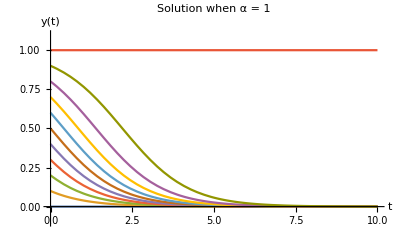

```mathematica
Plot[Evaluate[Table[y[t]/.sol[α,β]/.{α->1},{β,0,1,.1}]],{t,0,10},PlotRange->{-.1,1.1},PlotLabel->"Solution when α = 1",AxesLabel->{"t","y(t)"}]
```

Here’s we will do the same thing, but we will also show the equilibrium solutions on the plot as well.  The variable p1 represents the same plot as before, while p2 represents the equilibrium solutions.  The Show command allows us to display both plots on the same graph within the same Manipulate.

```mathematica
Manipulate[
p1 = Plot[Evaluate[Table[y[t]/.sol[α,β],{β,-1,2,.25}]],{t,0,5},PlotRange->{-.5,2.5},ExclusionsStyle->Directive[Black,Dashed]];
p2 = Plot[{0,α},{t,0,5},
PlotStyle->{{Black,Thick},{Black,Thick}},
PlotRange->{-1,2.5},
ExclusionsStyle->{None,None}];
Show[p1,p2],{α,1/2,3/2}]
```

## Plotting the Phase Line for various parameter values

```mathematica
F[y_,α_]=y^2 - α y;
```

```mathematica
Manipulate[
p3 = Plot[F[y,α],{y,-1,2.5},PlotRange->{-.3,.1}];
p4 = ListPlot[{{0,0},{α,0}},PlotStyle->{Red,PointSize[Large]}];
Show[p3,p4],{α,-1,3/2}]
```

```mathematica
Manipulate[
p1 = Plot[Evaluate[Table[y[t]/.sol[α,β],{β,-1,2,.25}]],{t,0,5},PlotRange->{-2,2.5},ExclusionsStyle->Directive[Black,Dashed]];
p2 = Plot[{0,α},{t,0,5},
PlotStyle->{{Black,Thick},{Black,Thick}},
PlotRange->{-1,2.5},
ExclusionsStyle->{None,None}];
PA=Show[p1,p2];
p3 = Plot[F[y,α],{y,-1,2.5},PlotRange->{-.3,.1}];
p4 = ListPlot[{{0,0},{A,0}},PlotStyle->{Red,PointSize[Large]}];
PB=Show[p3,p4];
GraphicsGrid[{{PA,PB}}],{α,-1,3/2}]
```

## Solving for the Equilibrium Points

Let’s define the function F(p,h) as well as the derivative with respect to p.  Notice that I take the derivative with respect to a separate variable “P” and then substitute in “p”.  This is so that the function FPrime returns the value of df/dp evaluated at p.

```mathematica
F[y_,α_]=y^2-α y
FPrime[y_,α_]=D[F[Y,α],Y]/.Y->y;
```

y^2-y α

```mathematica
eqPts[α_] = Solve[F[y,α]==0,y]
```

{{y→0},{y→α}}

We can evaluate f’(p,h) at the equilibrium points using the following:

```mathematica
Simplify[FPrime[y,α]/.eqPts[α][[1]]]
```

-α

```mathematica
Simplify[FPrime[y,α]/.eqPts[α][[2]]]
```

α

Note that eqPts[[1]] returns the first equilibrium point that the Solve command returned.  We can even plot both equilibrium points using the following command:

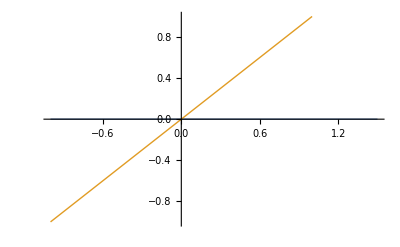

```mathematica
Plot[Evaluate[y/.eqPts[α]],{α,-1,3/2},PlotRange->{-1,1},PlotStyle->Thick]
```